```mathematica
SetDirectory["C:\Users\Ivan\Documents\INP_VEPP4M\INP_VEPP4M_betaFuctions"];
```

```mathematica
{name, first} = Transpose[Import["C:\\Users\\Ivan\\Documents\\Учеба\\Диплом\\Данные\\name.dat", "Table"]] ;
name
first
```

{stp0,stp2,stp4,srp1,srp2,srp3,srp4,srp5,srp6,srp7,srp8,srp9,sip1,sip2,srp10,srp11,srp12,srp13,srp14,srp15,srp16,srp17,sep5,sep4,sep3,sep1,sep0,nep0,nep1,nep3,nep4,nep5,nrp17,nrp16,nrp15,nrp14,nrp13,nrp12,nrp11,nrp10,nip3,nip1,nrp9,nrp8,nrp7,nrp6,nrp5,nrp4,nrp3,nrp2,nrp1,ntp4,ntp2,ntp0}

{9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
k=IntegerString[#, 10, 2] & /@ Range[10]
```

{01,02,03,04,05,06,07,08,09,10}

```mathematica
(* Load experiment data *)
ClearAll[load] ;
load[id_] := Block[
	{prefix},
	prefix = StringTemplate["C:\\Users\\Ivan\\Documents\\Учеба\\Диплом\\Данные\\`1`-n450-2000-10000-"][IntegerString[id, 10, 2]] ;
	Table[
		Take[N[Import[StringTemplate["`1``2`.dat"][prefix, name[[i]]], "CSV"]], {first[[i]]+1, first[[i]]+1 + 1023}],
		{i, 1, 54}
	]
] ;
dataExp = Table[load[i],{i,1,10}] ;
```

```mathematica
lenDat=10;
```

```mathematica
(*Beta from phase+(Ampl,Phase,Freq)*)
APF=Table[signalProc[dataExp[[i]],1,128],{i,1,lenDat}];
ClearAll[BFP];
BFP[bpm$bx_,bpm$fx_]:=Block[
{BFPX,DataBFPX,DataBFPX$StandartDeviation,BetaBPMs},
BFPX=Table[betaFromPhase[APF[[i]],bpm$bx,bpm$fx],{i,1,lenDat}];
DataBFPX=Table[BFPX[[i]][[j]],{j,1,54},{i,1,lenDat}];
BetaBPMs=Table[Around [Mean[DataBFPX[[i]]-bpm$bx[[i]]]/bpm$bx[[i]],StandardDeviation[(DataBFPX[[i]]-bpm$bx[[i]])/bpm$bx[[i]]]],{i,1,54}];
DataBFPX$StandartDeviation=Table[Around [Mean[DataBFPX[[i]]], StandardDeviation[DataBFPX[[i]]]],{i,1,54}];
{DataBFPX$StandartDeviation,BetaBPMs}
]
```

```mathematica
(*Phase and ampl*)
ClearAll[AaP];
AaP[APF_,bpm$fx_,ax_]:=Block[
{ampl,amplBPMs,deltphaseData,deltphase,phaseBPMs,bpm$fx1},
ampl=Table[APF[[i]][[j]][[1]],{j,1,54},{i,1,lenDat}];
deltphaseData=Table[Mod[APF[[i]][[Mod[id+1, 54, 1], 2]] - APF[[i]][[id, 2]] -If[id == 1, APF[[i]][[1, 3]]*2*Pi, 0]+If[id == 35, APF[[i]][[1, 3]]*2*Pi, 0]+If[id == 36, APF[[i]][[1, 3]]*2*Pi, 0]-If[id == 33, APF[[i]][[1, 3]]*2*Pi, 0], 2*Pi, -Pi],{i,1,lenDat},{id, 1, 54}];
deltphaseData=Table[Insert[Drop[deltphaseData[[i]],{9,10}],(Mod[APF[[i]][[Mod[11, 54, 1], 2]] - APF[[i]][[9, 2]], 2*Pi, -Pi]),9],{i,1,lenDat}];
deltphase=Table[deltphaseData[[i]][[j]],{j,1,53},{i,1,lenDat}];
bpm$fx1=Insert[Drop[bpm$fx,{9,10}],(Mod[bpm$fx[[11]]+bpm$fx[[9]],2*Pi,-Pi]),9];
phaseBPMs=Table[Around [Mean[deltphase[[i]]-bpm$fx1[[i]]]/bpm$fx1[[i]],StandardDeviation[(deltphase[[i]]-bpm$fx1[[i]])/bpm$fx1[[i]]]],{i,1,53}];
amplBPMs=Table[Around [Mean[ampl[[i]]-ax[[i]]]/ax[[i]],StandardDeviation[(ampl[[i]]-ax[[i]])/ax[[i]]]],{i,1,54}];
amplBPMs=Insert[Drop[amplBPMs,{10,10}],"non",10];
{phaseBPMs,amplBPMs}
]
```

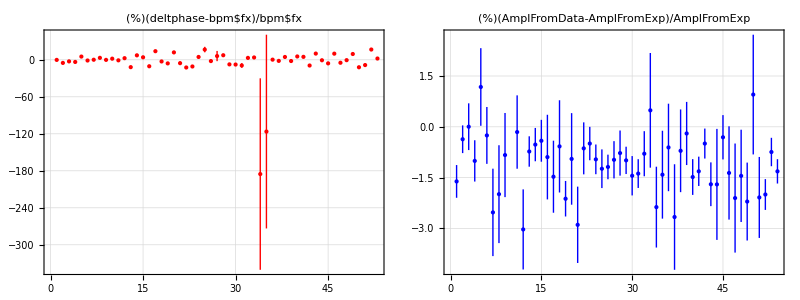

```mathematica
AaP[APF,bpm$fxN,ax][[2]];
{
ListPlot[AaP[APF,bpm$fxN,ax][[1]]*100,PlotRange->All, PlotStyle->Directive[PointSize[Medium],Red],PlotTheme->"Detailed",ImageSize -> 500,PlotLabel->"(%)(deltphase-bpm$fx)/bpm$fx",IntervalMarkersStyle->Red],  
ListPlot[AaP[APF,bpm$fxN,ax][[2]]*100,PlotRange->All, PlotStyle->Directive[PointSize[Medium],Blue],PlotTheme->"Detailed",ImageSize -> 500,PlotLabel->"(%)(AmplFromData-AmplFromExp)/AmplFromExp",IntervalMarkersStyle->Blue]
}//List//Grid
```

```mathematica
(*Beta from Ampl*)
ClearAll[BFA];
BFA[bpm$bx_]:=Block[
{BFAX,DataBFAX,DataBFAX$StandartDeviation,BetaBPMs},
BFAX=Table[Insert[betaFromAmpl[Drop[APF[[i]],{10,10}],Drop[bpm$bx,{10,10}]],"non",10],{i,1,lenDat}];
DataBFAX=Table[BFAX[[i]][[j]],{j,1,54},{i,1,lenDat}];
BetaBPMs=Table[Around [Mean[DataBFAX[[i]]-bpm$bx[[i]]]/bpm$bx[[i]],StandardDeviation[(DataBFAX[[i]]-bpm$bx[[i]])/bpm$bx[[i]]]],{i,1,54}];
DataBFAX$StandartDeviation=Table[Around [Mean[DataBFAX[[i]]], StandardDeviation[DataBFAX[[i]]]],{i,1,54}];
{DataBFAX$StandartDeviation,BetaBPMs}
]
```

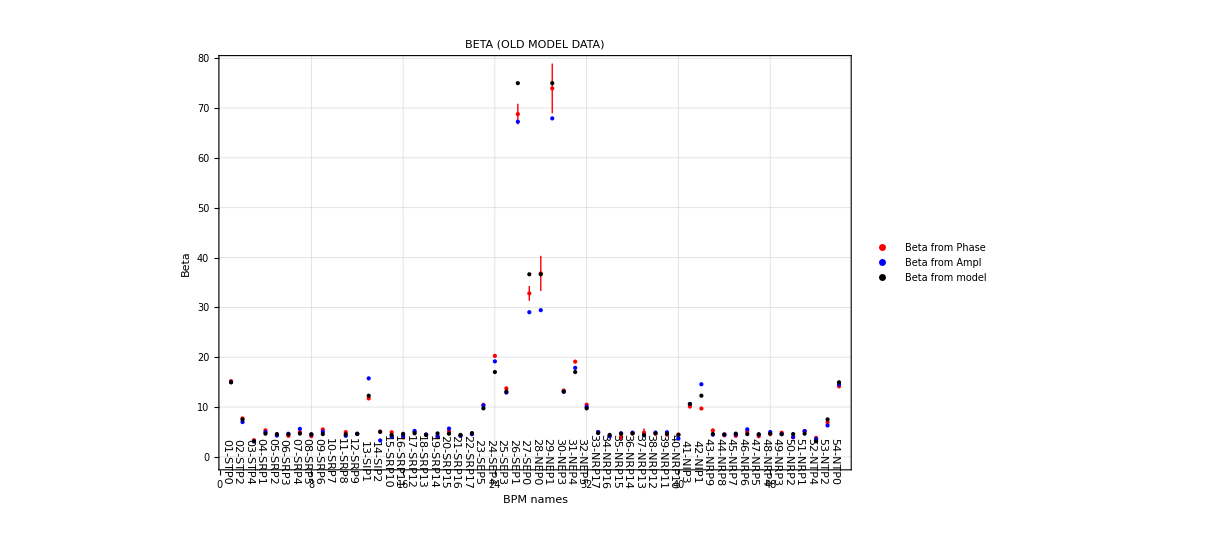
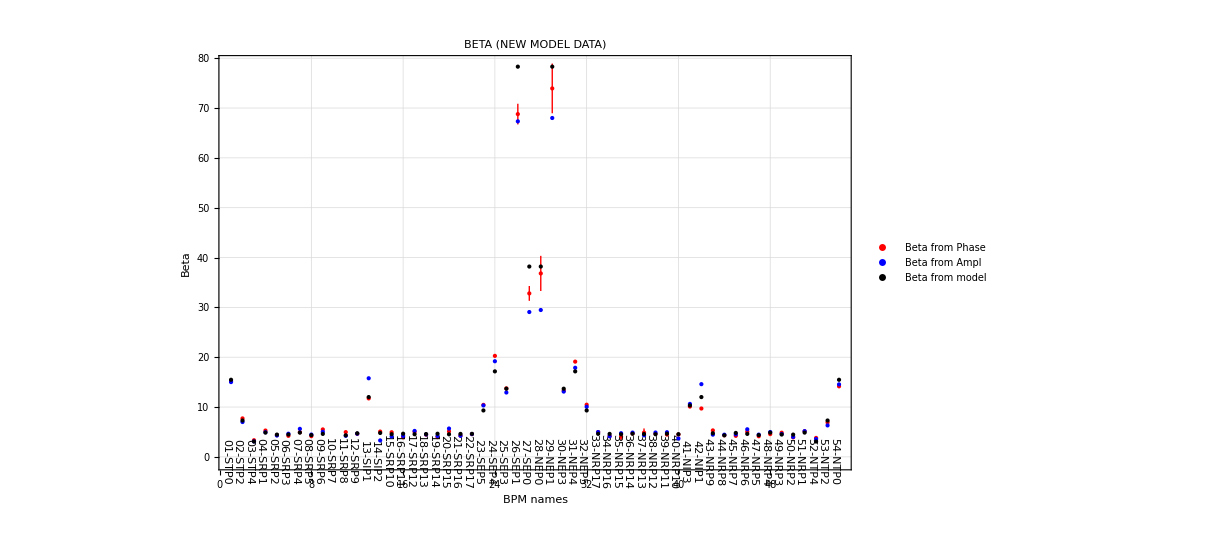
-Graphics- | -Graphics-

For new model data

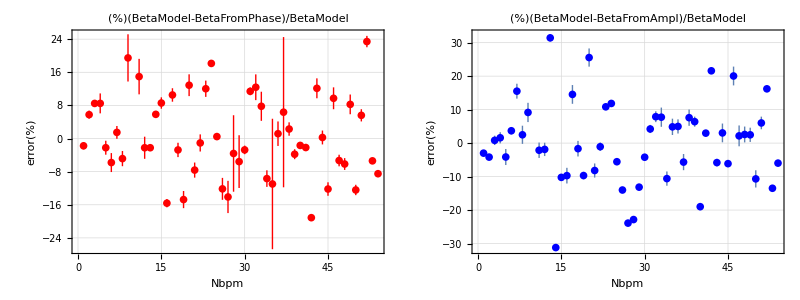

For old model data

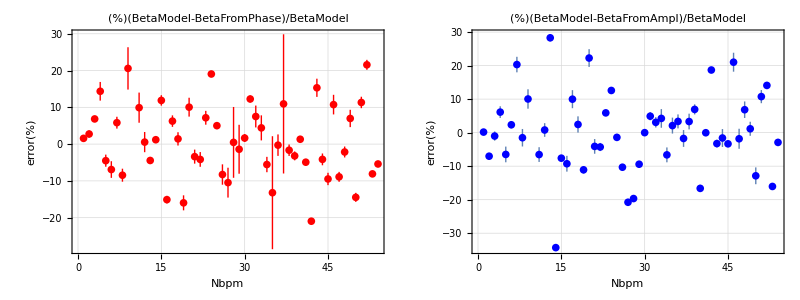

```mathematica
PlotBFF=Show[ListPlot[BFP[bpm$bx,bpm$fx][[1]],PlotRange->All,PlotStyle->Directive[PointSize[Medium],Red],IntervalMarkersStyle->Red,PlotLegends->{"Beta from Phase"},PlotTheme->"Detailed"]];
PlotBFA=Show[ListPlot[BFA[bpm$bx][[1]],PlotRange->All,PlotStyle->Directive[PointSize[Medium],Blue],IntervalMarkersStyle->Blue,PlotLegends->{"Beta from Ampl"},PlotTheme->"Detailed"]];
PlotBFFN=Show[ListPlot[BFP[bpm$bxN,bpm$fxN][[1]],PlotRange->All,PlotStyle->Directive[PointSize[Medium],Red],IntervalMarkersStyle->Red,PlotLegends->{"Beta from Phase"},PlotTheme->"Detailed"]];
PlotBFAN=Show[ListPlot[BFA[bpm$bxN][[1]],PlotRange->All,PlotStyle->Directive[PointSize[Medium],Blue],IntervalMarkersStyle->Blue,PlotLegends->{"Beta from Ampl"},PlotTheme->"Detailed"]];
{
plot$beta = Show[
	PlotBFF,
PlotBFA,
plot$bpm,
plotBetaModelX,
PlotRange->{All, {-10, All}},PlotLabel->"BETA (OLD MODEL DATA)",FrameLabel->{"BPM names", "Beta"},
	ImageSize -> 900
] ,
plot$betaN = Show[
	PlotBFFN,
PlotBFAN,
plot$bpm,
plotBetaModelXN,
PlotRange->{All, {-10, All}},PlotLabel->"BETA (NEW MODEL DATA)",FrameLabel->{"BPM names", "Beta"},
	ImageSize -> 900
] }//List//Grid
BFA[bpm$bxN][[2]];
Print[Style["For new model data",14,Black]]
{
ListPlot[BFP[bpm$bxN,bpm$fxN][[2]]*100,PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",PlotLabel->"(%)(BetaModel-BetaFromPhase)/BetaModel", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"},IntervalMarkersStyle->Red],
ListPlot[BFA[bpm$bxN][[2]]*100,PlotRange->All,PlotStyle->Blue,PlotTheme->"Detailed",PlotLabel->"(%)(BetaModel-BetaFromAmpl)/BetaModel", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"}]
}//List//Grid
Print[Style["For old model data",14,Black]]
{
ListPlot[BFP[bpm$bx,bpm$fx][[2]]*100,PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",PlotLabel->"(%)(BetaModel-BetaFromPhase)/BetaModel", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"},IntervalMarkersStyle->Red],
ListPlot[BFA[bpm$bx][[2]]*100,PlotRange->All,PlotStyle->Blue,PlotTheme->"Detailed",PlotLabel->"(%)(BetaModel-BetaFromAmpl)/BetaModel", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"}]
}//List//Grid
```